```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* Read the data file and reshape it *)
```

```mathematica
ncol=6;c=1.0;
data=ReadList["/home/romaingrvl/MEGAsync/thèse/freefem/spinning_mini_BS/bs_mat.out",Number];
data=data/.$Failed->0;
nline=Length[data]/ncol;
datashaped=ArrayReshape[data,{nline,ncol}]
```

```mathematica
(* Check the values of the grid bounds *)
```

```mathematica
xmin=Min[datashaped[[All,1]]]
xmax=Max[datashaped[[All,1]]]
θmin=Min[datashaped[[All,2]]]
θmax=Max[datashaped[[All,2]]]
```

0

1

0

1.5708

```mathematica
(* Useful things for later *)
```

```mathematica
gridx=DeleteDuplicates[datashaped[[All,1]]];
R[x_]:=c x/(1-x);
```

```mathematica
(* Construct tabulated values of the scalar field in compactified coordinates and interpolate *)
```

```mathematica
dataϕ=Table[{{datashaped[[i,1]],datashaped[[i,2]]},datashaped[[i,3]]},{i,nline}];
```

```mathematica
(* ϕ: scalar field profile in compactified coordinates 
ϕρz: scalar field profile in cylindrical coordinates *)
```

```mathematica
ϕ=Interpolation[dataϕ,InterpolationOrder->3]
ϕρz[ρ_,z_]:=ϕ[Sqrt[ρ^2+z^2]/(Sqrt[ρ^2+z^2]+c),ArcTan[z,ρ]]
```

InterpolatingFunction[…]

```mathematica
Plot3D[ϕ[x,θ],{x,xmin,xmax},{θ,θmin,θmax},PlotPoints->100,PlotRange->All,Mesh->None,BoundaryStyle->None,ColorFunction->ColorData[{"SunsetColors",{1.1,-0.5}}]]
```

-Graphics3D-

```mathematica
ρmax=5;zmax=ρmax;
Plot3D[ϕρz[ρ,z],{ρ,0,ρmax},{z,0,zmax},PlotPoints->100,PlotRange->All,Mesh->None,BoundaryStyle->None,ColorFunction->ColorData[{"SunsetColors",{1.1,-0.5}}]]
```

-Graphics3D-

```mathematica
(* Compute the coordinate distance (meaningful for dipolar stars only) *)
```

```mathematica
FindMaximum[{ϕ[x,θmin],0<=x<=1},{x,0.4}]
x0=%[[2,1,2]]
c x0/(1-x0)
%*2.0
```

{0.339304,{x→0.629571}}

0.629571

1.69957

3.39914

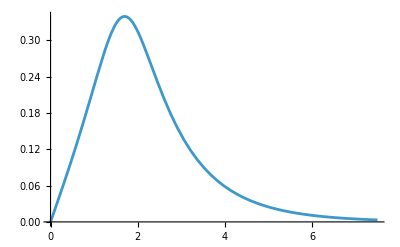

```mathematica
Plot[ϕρz[θmin,z],{z,0,1.5ρmax},PlotRange->All]
```

```mathematica
(* Construct tabulated values of ϕ-derivatives in compactified coordinates and interpolate *)
```

```mathematica
datadxϕ=Table[{{datashaped[[i,1]],datashaped[[i,2]]},datashaped[[i,4]]},{i,nline}];
```

```mathematica
dxϕ=Interpolation[datadxϕ,InterpolationOrder->3]
dxϕρz[ρ_,z_]:=dxϕ[Sqrt[ρ^2+z^2]/(Sqrt[ρ^2+z^2]+c),ArcTan[z,ρ]]
```

InterpolatingFunction[…]

```mathematica
Plot3D[dxϕ[x,θ],{x,xmin,xmax},{θ,θmin,θmax},PlotPoints->100,PlotRange->All,Mesh->None,BoundaryStyle->None,ColorFunction->ColorData[{"SunsetColors",{1.1,-0.5}}]]
```

-Graphics3D-

```mathematica
Plot3D[dxϕρz[ρ,z],{ρ,0,ρmax},{z,0,zmax},PlotPoints->100,PlotRange->All,Mesh->None,BoundaryStyle->None,ColorFunction->ColorData[{"SunsetColors",{1.1,-0.5}}]]
```

-Graphics3D-

```mathematica
(* Compute the coordinate distance (meaningful for dipolar stars only) *)
```

```mathematica
FindRoot[dxϕ[x,θmin],{x,x0}]
zcd=%[[1,2]]
c zcd/(1-zcd)
%*2
```

{x→0.629574}

0.629574

1.6996

3.39919

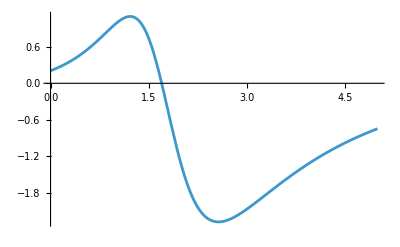

```mathematica
Plot[dxϕρz[θmin,z],{z,0,ρmax},PlotRange->All]
```

```mathematica
(* Construct tabulated values of F1 in compactified coordinates *)
```

```mathematica
dataF1=Table[{{datashaped[[i,1]],datashaped[[i,2]]},datashaped[[i,6]]},{i,nline}];
```

```mathematica
(* Takes only the values at θ=0 of the relevant line element for computing the distance *)
```

```mathematica
datadl=Cases[dataF1,{{x_,θmin},f_}:>{x, Exp[f]}];
dl=Interpolation[datadl,InterpolationOrder->3]
```

InterpolatingFunction[…]

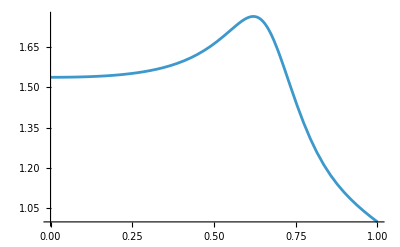

```mathematica
Plot[dl[x],{x,xmin,xmax},PlotRange->All]
```

```mathematica
(* Compute the proper distance from zcd *)
```

```mathematica
Lz=2NIntegrate[dl[x] c/(1-x)^2,{x,xmin,zcd}]
```

5.57732